# Lab 4 : Magnetic Fields and Ampere' s Law

Charlie Bushman
Phys 235 Lab #4
04-30-19

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
δQ[f_,p_,δ_]:=Sqrt[Sum[(D[f,p[[i]]] δ[[i]])^2,{i,1,Length[p]}]];
```

## Section A : Calibration of the Hall sensor

```mathematica
Clear[R,n,μ0,b,δR,δb,Vr1,Vr2,Vr3,Vr4,Vr5,Vr6,Vr7,Vr8]
data={{1.18,Vr1},{1.06,Vr2},{0.960,Vr3},{0.840,Vr4},{0.720,Vr5},{0.620,Vr6},{0.520,Vr7},{0.380,Vr8}};
δ1={0.04,0.02,0.02,0.02,0.02,0.02,0.02,0.02};
δ2={0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04};
f[x_]:={x[[1]],x[[2]]/R (n μ0)/(2 b)};
data1=Map[f,data];
δ2=Table[δQ[data1[[i,2]],{data[[i,2]],R,b},{δ2[[i]],δR,δb}],{i,1,Length[δ2]}];
R=10.3;δR=0.103;n=132;μ0=(4π) 10^-7;b=0.15;δb=0.005;
Vr1=4.72;Vr2=4.24;Vr3=3.72;Vr4=3.20;Vr5=2.72;Vr6=2.20;Vr7=1.72;Vr8=1.20;
data=data1;
displayData=Table[{data1[[i,1]] ± δ1[[i]],data1[[i,2]] ± δ2[[i]]},{i,1,Length[data1]}];
displayData//TableForm
```

1.18±0.04 | 0.000253377±9.07546×10^-6
1.06±0.02 | 0.00022761±8.20694×10^-6
0.96±0.02 | 0.000199695±7.27377×10^-6
0.84±0.02 | 0.000171781±6.35209×10^-6
0.72±0.02 | 0.000146014±5.51649×10^-6
0.62±0.02 | 0.000118099±4.6371×10^-6
0.52±0.02 | 0.0000923323±3.86468×10^-6
0.38±0.02 | 0.0000644179±3.10426×10^-6

{-0.0000297087+0.00024072 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0000297087 | 2.88478×10^-6 | -10.2984 | 0.0000489671
x | 0.00024072 | 3.6961×10^-6 | 65.1281 | 8.81217×10^-10}

0.00024072 V/T±3.6961×10^-6 V/T

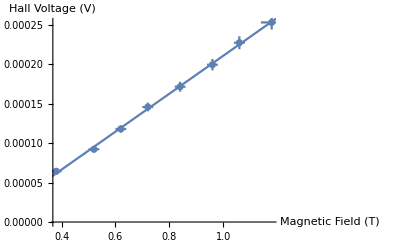

```mathematica
fit=LinearModelFit[data,x,x,Weights->1/(δ1^2+δ2^2),IncludeConstantBasis->True];
fit[{"BestFit","ParameterTable"}]
propConst=fit[[1,2,2]];
δpropConst=3.6961*^-6;
propConst "V/T" ± δpropConst "V/T"
Show[ErrorListPlot[Table[{{data[[i,1]],data[[i,2]]},ErrorBar[δ1[[i]],δ2[[i]]]},{i,1,Length[data]}]],Plot[fit[x],{x,0,2}],AxesLabel->{"Magnetic Field (T)","Hall Voltage (V)"},ImageSize->Full]
```

## Section B : Ampere’s Law

### Section B .1: Infinite Loop

```mathematica
tempPropConst=propConst;tempδProp=δpropConst;
Clear[Vr1,Vr2,Vr3,Vr4,Vr5,Vr6,propConst,δPropConst]
data={{0.05,Vr1},{0.05,Vr2},{0.05,Vr3},{0.05,Vr4},{0.05,Vr5},{0.05,Vr6}};
δ1={0.005,0.005,0.005,0.005,0.005,0.005};
δ2={0.02,0.02,0.02,0.02,0.02,0.02};
f[x_]:={x[[1]],propConst x[[2]]};
data1=Map[f,data];
δ2=Table[δQ[data1[[i,2]],{data[[i,2]],propConst},{δ2[[i]],δPropConst}],{i,1,Length[δ2]}];
propConst=tempPropConst;δPropConst=tempδProp;
Vr1=1.10;Vr2=0.840;Vr3=0.580;Vr4=0.400;Vr5=0.300;Vr6=0.240;
data=data1;
displayData=Table[{data1[[i,1]] ± δ1[[i]],data1[[i,2]] ± δ2[[i]]},{i,1,Length[data1]}];
displayData//TableForm
```

0.05±0.005 | 0.000264792±6.30146×10^-6
0.05±0.005 | 0.000202204±5.72867×10^-6
0.05±0.005 | 0.000139617±5.2701×10^-6
0.05±0.005 | 0.0000962878±5.03628×10^-6
0.05±0.005 | 0.0000722159±4.94043×10^-6
0.05±0.005 | 0.0000577727±4.89543×10^-6

```mathematica
(*Factor of two out front accounts for the negative side of the loop*)
lineIntegral=2 Sum[data[[i,1]] data[[i,2]],{i,1,Length[data]}];
δlineIntegral=2 Sum[Sqrt[(data[[i,2]] δ1[[i]])^2+(data[[i,1]] δ2[[i]])^2],{i,1,Length[δ1]}];
lineIntegral*10^6 "μT*m" ± δlineIntegral*10^6 "μT*m"
```

83.289 μT*m±9.03468 μT*m

```mathematica
(*Theoretical value: line integral of magnetic field over z-axis*)
ic=0.458;
theorLineInt=Integrate[(n μ0 ic b^2)/(2(b^2+z^2)^(3/2)),{z,-∞,∞}];
δB=δQ[(n μ0 tic tb^2)/(2(tb^2+tz^2)^(3/2)),{tic,tb},{δtic,δtb}];
tic=ic;tb=b;δtic=0.006;δtb=δb;
δtheorLineInt=NIntegrate[δB,{tz,-∞,∞}];
theorLineInt*10^6 "μT*m" ± δtheorLineInt*10^6 "μT*m"
Clear[tic,tb,tz,δtic,δtb]
```

75.9713 μT*m±2.26942 μT*m

### Section B .2 : Loop around Coil

```mathematica
tempPropConst=propConst;tempδProp=δpropConst;
Clear[Vr1,Vr2,Vr3,Vr4,Vr5,Vr6,Vr7,propConst,δPropConst]
data={{0.01,Vr1},{0.01,Vr2},{0.01,Vr3},{0.01,Vr4},{0.01,Vr5},{0.01,Vr6},{0.01,Vr7}};
δ1={0.002,0.002,0.002,0.002,0.002,0.002,0.002};
δ2={0.02,0.02,0.02,0.02,0.02,0.02,0.02};
f[x_]:={x[[1]],propConst x[[2]]};
data1=Map[f,data];
δ2=Table[δQ[data1[[i,2]],{data[[i,2]],propConst},{δ2[[i]],δPropConst}],{i,1,Length[δ2]}];
propConst=tempPropConst;δPropConst=tempδProp;
Vr1=0.074;Vr2=0.920;Vr3=0.880;Vr4=1.00;Vr5=0.920;Vr6=0.860;Vr7=0.760;
data=data1;
displayData=Table[{data1[[i,1]] ± δ1[[i]],data1[[i,2]] ± δ2[[i]]},{i,1,Length[data1]}];
displayData//TableForm
lineIntegral1=Sum[data[[i,1]] data[[i,2]],{i,1,Length[data]}]
δlineIntegral1=Sum[Sqrt[(data[[i,2]] δ1[[i]])^2+(data[[i,1]] δ2[[i]])^2],{i,1,Length[δ1]}]
```

0.01±0.002 | 0.0000178133±4.82215×10^-6
0.01±0.002 | 0.000221462±5.89416×10^-6
0.01±0.002 | 0.000211833±5.81013×10^-6
0.01±0.002 | 0.00024072±6.06956×10^-6
0.01±0.002 | 0.000221462±5.89416×10^-6
0.01±0.002 | 0.000207019±5.76907×10^-6
0.01±0.002 | 0.000182947±5.57396×10^-6

0.0000130326

2.65465×10^-6

```mathematica
tempPropConst=propConst;tempδProp=δpropConst;
Clear[Vr1,Vr2,Vr3,Vr4,Vr5,Vr6,Vr7,Vr8,Vr9,Vr10,propConst,δPropConst]
data={{0.01,Vr1},{0.01,Vr2},{0.01,Vr3},{0.01,Vr4},{0.01,Vr5},{0.01,Vr6},{0.01,Vr7},{0.01,Vr8},{0.01,Vr9},{0.01,Vr10}};
δ1={0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002};
δ2={0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02};
f[x_]:={x[[1]],propConst x[[2]]};
data1=Map[f,data];
δ2=Table[δQ[data1[[i,2]],{data[[i,2]],propConst},{δ2[[i]],δPropConst}],{i,1,Length[δ2]}];
propConst=tempPropConst;δPropConst=tempδProp;
Vr1=0.460;Vr2=0.620;Vr3=0.520;Vr4=0.900;Vr5=1.06;Vr6=0.980;Vr7=0.760;
Vr8=0.640;
Vr9=0.440;
Vr10=0.180;
data=data1;
displayData=Table[{data1[[i,1]] ± δ1[[i]],data1[[i,2]] ± δ2[[i]]},{i,1,Length[data1]}];
displayData//TableForm
lineIntegral2=Sum[data[[i,1]] data[[i,2]],{i,1,Length[data]}]
δlineIntegral2=Sum[Sqrt[(data[[i,2]] δ1[[i]])^2+(data[[i,1]] δ2[[i]])^2],{i,1,Length[δ1]}]
```

0.01±0.002 | 0.000110731±5.10579×10^-6
0.01±0.002 | 0.000149246±5.33195×10^-6
0.01±0.002 | 0.000125174±5.18385×10^-6
0.01±0.002 | 0.000216648±5.85183×10^-6
0.01±0.002 | 0.000255163±6.2071×10^-6
0.01±0.002 | 0.000235905±6.02483×10^-6
0.01±0.002 | 0.000182947±5.57396×10^-6
0.01±0.002 | 0.000154061±5.36414×10^-6
0.01±0.002 | 0.000105917±5.08165×10^-6
0.01±0.002 | 0.0000433295±4.86014×10^-6

0.0000157912

3.21318×10^-6

```mathematica
tempPropConst=propConst;tempδProp=δpropConst;
Clear[Vr1,Vr2,Vr3,Vr4,Vr5,Vr6,Vr7,propConst,δPropConst]
data={{0.01,Vr1},{0.01,Vr2},{0.01,Vr3},{0.01,Vr4},{0.01,Vr5},{0.01,Vr6},{0.01,Vr7}};
δ1={0.002,0.002,0.002,0.002,0.002,0.002,0.002};
δ2={0.02,0.02,0.02,0.02,0.02,0.02,0.02};
f[x_]:={x[[1]],propConst x[[2]]};
data1=Map[f,data];
δ2=Table[δQ[data1[[i,2]],{data[[i,2]],propConst},{δ2[[i]],δPropConst}],{i,1,Length[δ2]}];
propConst=tempPropConst;δPropConst=tempδProp;
Vr1=0.760;Vr2=0.880;Vr3=0.920;Vr4=1.04;Vr5=0.900;Vr6=0.820;Vr7=0.640;
data=data1;
displayData=Table[{data1[[i,1]] ± δ1[[i]],data1[[i,2]] ± δ2[[i]]},{i,1,Length[data1]}];
displayData//TableForm
lineIntegral3=Sum[data[[i,1]] data[[i,2]],{i,1,Length[data]}]
δlineIntegral3=Sum[Sqrt[(data[[i,2]] δ1[[i]])^2+(data[[i,1]] δ2[[i]])^2],{i,1,Length[δ1]}]
```

0.01±0.002 | 0.000182947±5.57396×10^-6
0.01±0.002 | 0.000211833±5.81013×10^-6
0.01±0.002 | 0.000221462±5.89416×10^-6
0.01±0.002 | 0.000250348±6.1607×10^-6
0.01±0.002 | 0.000216648±5.85183×10^-6
0.01±0.002 | 0.00019739±5.68895×10^-6
0.01±0.002 | 0.000154061±5.36414×10^-6

0.0000143469

2.89789×10^-6

```mathematica
tempPropConst=propConst;tempδProp=δpropConst;
Clear[Vr1,Vr2,Vr3,Vr4,Vr5,Vr6,Vr7,Vr8,Vr9,Vr10,propConst,δPropConst]
data={{0.01,Vr1},{0.01,Vr2},{0.01,Vr3},{0.01,Vr4},{0.01,Vr5},{0.01,Vr6},{0.01,Vr7},{0.01,Vr8},{0.01,Vr9},{0.01,Vr10}};
δ1={0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002,0.002};
δ2={0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02};
f[x_]:={x[[1]],propConst x[[2]]};
data1=Map[f,data];
δ2=Table[δQ[data1[[i,2]],{data[[i,2]],propConst},{δ2[[i]],δPropConst}],{i,1,Length[δ2]}];
propConst=tempPropConst;δPropConst=tempδProp;
Vr1=1.02;Vr2=1.20;Vr3=1.58;Vr4=1.82;Vr5=2.04;Vr6=2.04;Vr7=1.84;Vr8=1.60;Vr9=1.42;Vr10=1.24;
data=data1;
displayData=Table[{data1[[i,1]] ± δ1[[i]],data1[[i,2]] ± δ2[[i]]},{i,1,Length[data1]}];
displayData//TableForm
lineIntegral4=Sum[data[[i,1]] data[[i,2]],{i,1,Length[data]}]
δlineIntegral4=Sum[Sqrt[(data[[i,2]] δ1[[i]])^2+(data[[i,1]] δ2[[i]])^2],{i,1,Length[δ1]}]
```

0.01±0.002 | 0.000245534±6.11485×10^-6
0.01±0.002 | 0.000288864±6.54602×10^-6
0.01±0.002 | 0.000380337±7.56849×10^-6
0.01±0.002 | 0.00043811±8.27222×10^-6
0.01±0.002 | 0.000491068±8.94598×10^-6
0.01±0.002 | 0.000491068±8.94598×10^-6
0.01±0.002 | 0.000442924±8.33244×10^-6
0.01±0.002 | 0.000385151±7.62568×10^-6
0.01±0.002 | 0.000341822±7.12213×10^-6
0.01±0.002 | 0.000298492±6.64709×10^-6

0.0000380337

7.64508×10^-6

```mathematica
lineIntegral=lineIntegral1+lineIntegral2+lineIntegral3+lineIntegral4;
δlineIntegral=δlineIntegral1+δlineIntegral2+δlineIntegral3+δlineIntegral4;
lineIntegral*10^6 "μT*m" ± δlineIntegral*10^6 "μT*m"
```

81.2043 μT*m±16.4108 μT*m